# Lección 4 - Programación con reglas

## Patrones

MatchQ

```mathematica
MatchQ[{a,x,b},{_,x,_}]
```

True

```mathematica
MatchQ[{a,b,c},{_,x,_}]
```

False

```mathematica
MatchQ[{a,🐺},{_,_}]
```

True

```mathematica
MatchQ[{a,a,a},{_,_}]
```

False

Cases

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{_,_}]
```

{{a,a},{b,a},{b,b},{c,a}}

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{b,_}]
```

{{b,a},{b,b}}

```mathematica
MatchQ[#,{b,_}]&/@{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}}
```

{False,True,False,True,False,False}

Select

```mathematica
Select[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},MatchQ[#,{b,_}]&]
```

{{b,a},{b,b}}

Alternatives

```mathematica
Alternatives[a,b]
```

a|b

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{a|b,_}]
```

{{a,a},{b,a},{b,b}}

```mathematica
IntegerDigits[Range[100,500,55]]
```

{{1,0,0},{1,5,5},{2,1,0},{2,6,5},{3,2,0},{3,7,5},{4,3,0},{4,8,5}}

```mathematica
Cases[IntegerDigits[Range[100,500,55]],{_,_,5}]
```

{{1,5,5},{2,6,5},{3,7,5},{4,8,5}}

```mathematica
Cases[IntegerDigits[Range[100,500,55]],{_,1|2,_}]
```

{{2,1,0},{3,2,0}}

Doble guión bajo o “Double blank” ( __ )

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,1,b},{1,2,3,4,🐺,b},{b}},{__,b}]
```

{{b,b},{b,1,b},{1,2,3,4,🐺,b}}

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{__,a|b}|{c,__}]
```

{{a,a},{b,a},{b,b},{c,a},{b,b,b}}

Generalización

```mathematica
Cases[{f[1],g[2,3],{a,b,c},f[x],f[x,x]},f[_]]
```

{f[1],f[x]}

Reemplazo ( /. )

```mathematica
ReplaceAll[{a,b,a,a,b,b,a,b},b->Red]
```

{a,RGBColor[1, 0, 0],a,a,RGBColor[1, 0, 0],RGBColor[1, 0, 0],a,RGBColor[1, 0, 0]}

```mathematica
{a,b,a,a,{{b}},{b},{a,b,1+b},b}/. 1->Red
```

{a,b,a,a,{{b}},{b},{a,b,b+RGBColor[1, 0, 0]},b}

```mathematica
Replace[{a,b,a,a,b,{b},a,b},b->Red,2]
```

{a,RGBColor[1, 0, 0],a,a,RGBColor[1, 0, 0],{RGBColor[1, 0, 0]},a,RGBColor[1, 0, 0]}

```mathematica
{{1,a},{1,b},{1,a,b},{2,b,c},{2,b}}/. {1,_}->Red
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],{1,a,b},{2,b,c},{2,b}}

Patrones nombrados

```mathematica
Cases[{{a,a,a},{a,a},{a,b},{a,c},{b,a},{b,b},{c},{a},{b}},{_,_}]
```

{{a,a},{a,b},{a,c},{b,a},{b,b}}

```mathematica
Cases[{{a,a,a},{a,a},{a,b},{a,c},{b,a},{b,b},{c},{a},{b}},{h_,h_}]
```

{{a,a},{b,b}}

Reglas de reemplazo

```mathematica
{{1,RGBColor[1, 0, 0]},{1,RGBColor[0, 0, 1]},{1,RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{2,RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{2,RGBColor[0, 0, 1]}}/. {{1,x_}->{x,x,Yellow,x,x},{2,y__}->{🐺,y,🐺}}
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{1,RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{🐺,RGBColor[0, 1, 0],RGBColor[0, 0, 1],🐺},{🐺,RGBColor[0, 0, 1],🐺}}

```mathematica
{f[1],g[2],f[2],f[6],g[3]}/. f[x_]->x+10
```

{11,g[2],12,16,g[3]}

```mathematica
Cases[{f[1],g[2],f[2],f[6],g[3]},f[x_]->x+10]
```

{11,12,16}

## Sublenguaje de patrones

Head

```mathematica
digitback[n_Integer] := Framed[Reverse[IntegerDigits[n]]]
```

```mathematica
{digitback[1234],digitback[6712],digitback[x],digitback[{4,3,2}],digitback[2^32]}
```

{{4,3,2,1},{2,1,7,6},digitback[x],digitback[{4,3,2}],{6,9,2,7,6,9,4,9,2,4}}

Condition

```mathematica
pdigitback[n_Integer/;n>0]:=Framed[Reverse[IntegerDigits[n]]]
```

```mathematica
{pdigitback[1234],pdigitback[-1234],pdigitback[x],pdigitback[2^40]}
```

{{4,3,2,1},pdigitback[-1234],pdigitback[x],{6,7,7,7,2,6,1,1,5,9,9,0,1}}

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[x_,y_]:=Green/;x<=y
```

```mathematica
{check[1,2],check[2,1],check[3,4],check[50,60],check[60,50]}
```

{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

Doble y triple guión bajo (___)

```mathematica
blackwhite[{___,Black,m___,White,___}]:={1,m,2,m,3,m,4}
```

```mathematica
blackwhite[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],4}

```mathematica
blackwhitex[{___,Black,Longest[m___],White,___}]:={1,m,2,m,3,m,4}
```

```mathematica
blackwhitex[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],4}

```mathematica
{a,b,c,d,e,f,g}/. {x__,Shortest[y__]}:>{{x},{y}}
```

{{a,b,c,d,e,f},{g}}

```mathematica
{a,b,c,d,e,f,g}/. {x__,y__}:>{{x},{y}}
```

{{a},{b,c,d,e,f,g}}

Repeated

```mathematica
MatchQ[{a,a,a},{a..}]
```

True

```mathematica
MatchQ[{a,a,b,a},{(a|b)..}]
```

True

```mathematica
bwcut[{a___,Longest[(Black|White)..],b___}]:={{a},Red,{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},RGBColor[1, 0, 0],{RGBColor[1, 1, 0]}}

Named arguments

```mathematica
grid22[m:{{_,_},{_,_}}]:=Grid[m,Frame->All]
```

```mathematica
grid22[{{a,b},{c,d}}]
```

a | b
c | d

```mathematica
{grid22[{{a,b},{c,d}}],grid22[{{12,34},{56,78}}],grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}
```

{a | b
c | d,12 | 34
56 | 78,grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}

```mathematica
bwcut[{a___,r:Longest[(Black|White)..],b___}]:={{a},Framed[Length[{r}]],{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},5,{RGBColor[1, 1, 0]}}

Iteración

```mathematica
{5,4,1,3,2}/. {x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{4,5,1,3,2}

```mathematica
{5,4,1,3,2}//. {x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{1,2,3,4,5}

```mathematica
NestList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2},10]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
Transpose[%]
```

{{4,4,1,1,1,1,1,1,1},{5,1,4,4,3,3,3,2,2},{1,5,5,3,4,4,2,3,3},{3,3,3,5,5,2,4,4,4},{2,2,2,2,2,5,5,5,5}}

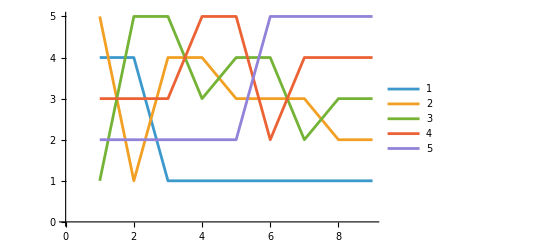

```mathematica
ListLinePlot[%,PlotLegends->Automatic]
```

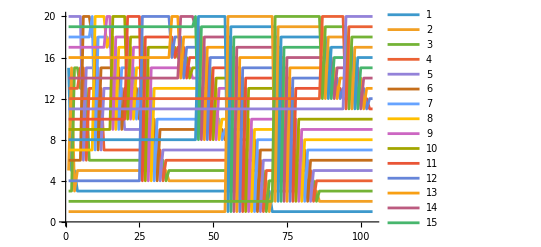

```mathematica
ListLinePlot[Transpose[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[20]]]],PlotLegends->Automatic]
```

## Tarea

Ejercicios del capítulo 32 y 41.